Task1

6. ∫_-1^3 (ln (x + 3) sin (x))/x^2ⅆx

Interval[{-1,3}]

Integral by Simpson formula = 0.870583499

Iterations number = 6

Integral by NIntegrate formula = 0.870583505

Integral by Gauss formula = 0.870583505

Iterations number = 5

Integral by NIntegrate formula = 0.870583505

--------------------------------------------------------------

Task2

TraditionalForm`6

Min with Minimize[]:

{-0.837962,{x→0.348331}}

Max with Maximize:

{7.5716,{x→2.66124}}

xMin with bisection method = {0.348330102,-0.837962}

Iterations: 22

xMax with bisection method = {2.66123484,7.5716}

Iterations: 22

xMin with golden ratio method = {0.348330513,-0.837962}

Iterations: 30

xMax with golden ratio method = {2.66123563,7.5716}

Iterations: 30

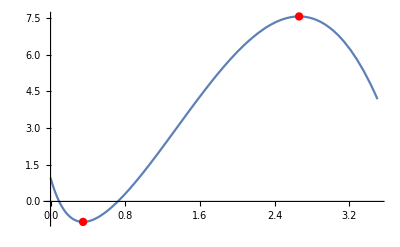

```mathematica
Style[Text["Task1"], FontSize->25]
(*С помощью формул Симпсона и Гаусса вычислить интеграл с точностью до 10^-6. Сравнить полученные результаты и результат вычисления с помощью встроенной функции. Должны быть собственные функции, аргументами которых являются интегрируемая функция и интервал. Кроме значений интеграла должно выводиться количество итераций, необходимых для вычисления. В формуле Гаусса для получения полиномов Лежандра должна быть написана собственная функция.*)
Text["6. ∫_-1^3 (ln (x + 3) sin (x))/x^2ⅆx"]
Clear[h,f,n,a,b, segment]
f[x_]:= (Log[x+30]*Sin[x])/(x^2+3);
a=-1;
b=3;
h=(a+b)/2;
n=2;
eps = 10^-6;
segment = Interval[{a,b}]

SimpInt[h_,n_,f_,segment_]:=Module[{k,resInt,a,b},
resInt=0;
a=First[First[segment]];
b=Last[Last[segment]];
For[k=0,k≤n-1,k++,
resInt+=f[a+k*h]+4*f[(a+k*h+a+(k+1)*h)/2]+f[a+(k+1)*h];
];
resInt=resInt*h/6;
Return[resInt];
];
SimpsonIterations[f_,segment_]:=Module[{iterations,Int,prevInt,r,eps,h,n,a,b},
iterations=0;
Int=0;
prevInt=1;
r=Abs[Int-prevInt];
eps=10^-6;
a=First[First[segment]];
b=Last[Last[segment]];
h=(b-a)/2;
n=2;
While[r≥eps,
prevInt=Int;
Int=SimpInt[h,n,f,segment];
h/=2;
n*=2;
iterations++;
r=Abs[Int-prevInt]
];
Print["Integral by Simpson formula = ",NumberForm[N[Int],9]];
Print["Iterations number = ",iterations];
Print["Integral by NIntegrate formula = ",NumberForm[NIntegrate[f[t],{t,a,b}],9]];
];
Lejandr[i_,segment_,h_,n_]:=Module[{a,P,w},
a=First[First[segment]];

P=1/(2^n*Factorial[n])*(D[(z^2-1)^n,{z,n}]);
w=(2/((1-z^2)*(D[P])^2))(*/.z->(a+i*h)*);
Return[P];
];
GaussInt[f_,segment_,h_,n_]:=Module[{k,resInt,a,b,a1,b1,h1,segment1,w,xVect},
resInt=0;
a=First[First[segment]];
b=Last[Last[segment]];
a1=-1;
b1=1;
h1=(b1-a1)/n;
segment1=Interval[{a1,b1}];
P=Lejandr[k,segment1,h1,n];
(*Print[P];*)
xVect=Solve[P==0,z];
zeros={z}/.Solve[P==0,z];
For[k=1,k≤n,k++,
w=2/((1-First[zeros[[k]]]^2)*(D[P,z]/.z->First[zeros[[k]]])^2);
resInt+=w*f[(a+b)/2+((b-a)/2)*First[zeros[[k]]]];
];
resInt=resInt*(b-a)/2;
Return[resInt];
];
GaussIterations[f_,segment_]:=Module[{iterations,a,b,h,n,r,eps,Int,prevInt},
iterations=0;
a=First[First[segment]];
b=Last[Last[segment]];
h=(b-a)/2;
n=2;
Int=0;
prevInt=1;
r=Abs[Int-prevInt];
eps=10^-6;
While[r≥eps,
prevInt=Int;
Int=GaussInt[f,segment,h,n];
h/=2;
n*=2;
iterations++;
r=Abs[Int-prevInt]
];
Print["Integral by Gauss formula = ",NumberForm[N[Int],9]];
Print["Iterations number = ",iterations];
Print["Integral by NIntegrate formula = ",NumberForm[NIntegrate[f[t],{t,a,b}],9]];
];
SimpsonIterations[f,segment]
GaussIterations[f,segment]
Print["--------------------------------------------------------------"]
Style[Text["Task2"<>], FontSize->25]
(*Методами деления отрезка пополам и золотого сечения вычислить максимум и минимум функции на заданном интервале с точностью до 10^-6. Сравнить полученные результаты и результат вычисления с помощью встроенных функций Maximize и Minimize. Должны быть собственные функции, аргументами которых являются заданная функция и интервал. Выводиться должно количество итераций, требуемых для вычисления min и max, и {Subscript[x, min],min(f(x))},{Subscript[x, max],max(f(x))} . Точки максимума и минимума должны быть изображены графически.*)



Text["TraditionalForm`6"]
Clear[segment2,f1]
f1[x_]:=ⅇ^(1-5x)-x^3+4 x^2-2+1/(x^2+4)/;0≤x≤7/2
segment2=Interval[{0,7/2}];
Bisection[f1_,segment2_]:=Module[{a,b,d,l,r,eps,j,xMin,xMax,iterations,err,solMin,solMax},
eps=10^-6;
d=eps/2-eps/4;
a=First[First[segment2]];
b=Last[Last[segment2]];
iterations=0;
err=(b-a)/2;
While[err≥eps,
xMin=(a+b)/2;
l=xMin-d;
r=xMin+d;
If[f1[l]≤f1[r],
b=r,
a=l
];
err=(b-a)/2;
iterations++;
];
solMin={NumberForm[N[xMin],9],N[f1[xMin]]};
Print["xMin with bisection method = ",solMin];
Print["Iterations: ",iterations];

a=First[First[segment2]];
b=Last[Last[segment2]];
iterations=0;
err=(b-a)/2;
While[err≥eps,
xMax=(a+b)/2;
l=xMax-d;
r=xMax+d;
If[f1[l]≤f1[r],
a=l,
b=r
];
err=(b-a)/2;
iterations++;
];
solMax={NumberForm[N[xMax],9],N[f1[xMax]]};
Print["xMax with bisection method = ",solMax];
Print["Iterations: ",iterations];

];
GoldenRatioIterations[f1_,segment2_]:=Module[{a,b,l,r,err,eps,d,xMin,xMax,solMin,solMax,iterations},
a=First[First[segment2]];
b=Last[Last[segment2]];
iterations=0;
err=(b-a)/2;
d=(Sqrt[5]-1)/2;
eps=10^-6;
While[err≥eps,
xMin=(a+b)/2;
l=b-d*(b-a);
r=a+d*(b-a);
If[f1[l]<f1[r],
b=r,
a=l
];
err=(b-a)/2;
iterations++;
];
solMin={NumberForm[N[xMin],9],N[f1[xMin]]};
Print["xMin with golden ratio method = ",solMin];
Print["Iterations: ",iterations];
a=First[First[segment2]];
b=Last[Last[segment2]];
iterations=0;
err=(b-a)/2;
While[err≥eps,
xMax=(a+b)/2;
l=b-d*(b-a);
r=a+d*(b-a);
If[f1[l]<f1[r],
a=l,
b=r
];
err=(b-a)/2;
iterations++;
];
solMax={NumberForm[N[xMax],9],N[f1[xMax]]};
Print["xMax with golden ratio method = ",solMax];
Print["Iterations: ",iterations];
a=First[First[segment2]];
b=Last[Last[segment2]];
points={{xMin,f1[xMin]},{xMax,f1[xMax]}};
Plot[f1[x],{x,a,b},Epilog->{Red,PointSize[0.015],Point[points]}]
];

Print["Min with Minimize[]: "]
N[Minimize[{ⅇ^(1-5x)-x^3+4 x^2-2+1/(x^2+4),x≥0,x≤7/2},x]]
Print["Max with Maximize: "]
N[Maximize[{ⅇ^(1-5x)-x^3+4 x^2-2+1/(x^2+4),x≥0,x≤7/2},x]]
Bisection[f1,segment2]
GoldenRatioIterations[f1,segment2]
```